```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
FStar = FSS
HStar =HSS
RStar = RSS
FIStar = FSS/.{λ->λ2,σ->σ2,ρ->ρ2,β->β2,δ->δ2};
HIStar=HSS/.{λ->λ2,σ->σ2,ρ->ρ2,β->β2,δ->δ2};
RIStar=RSS/.{λ->λ2,σ->σ2,ρ->ρ2,β->β2,δ->δ2};
SolutionsF ={FStar,FIStar}
SolutionsR ={RStar,RIStar}
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

(μ (-λ+σ))/(2 λ ρ+μ σ)

{-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),-(α λ2 μ^2 (μ+2 ρ2) (λ2-σ2))/((2 λ2 ρ2+μ σ2) (λ2 (2 δ2 λ2+2 β2 μ-λ2 μ) ρ2+μ (β2 μ+λ2 (δ2+ρ2)) σ2))}

{(μ (-λ+σ))/(2 λ ρ+μ σ),(μ (-λ2+σ2))/(2 λ2 ρ2+μ σ2)}

```mathematica
StarvationThreshold = Table[{10^i,-f0*m^1.19/m/.m->10^i},{i,-2,9,0.001}];
```

```mathematica
γ-1
```

0.19

```mathematica
m^1.19/m
```

m^0.19

```mathematica
Invade = ParallelTable[
M = 10^MassExp;
chimin=Quiet[chi/.Solve[(1-0.0202 m^0.18999999999999995)/(1+chi)==1/.m->10^MassExp,chi][[1]]];
tic = (MassExp-0)/0.001 +1;
values ={α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality,λ2->InvaderConsumerGrowth,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderFullMaintenance,δ2->InvaderStarveMaintenance};
FSol =dimSS[ SolutionsF[[1]]]/.values;
FISol = dimSSInvader[SolutionsF[[2]]]/.values;
RSol = dimRSS[ SolutionsR[[1]]]/.values;
RISol = dimRSS[ SolutionsR[[2]]]/.values;
ChiRange = Table[x,{x,chimin+0.001,0.05,0.0001}];
Test = Table[(Re[RISol]<Re[RSol]),{chi,ChiRange}];
ChiHigher=ChiRange[[Flatten[Position[Test,True],1]]];
{M,ChiHigher},
{MassExp,-2,9,0.01}];
```

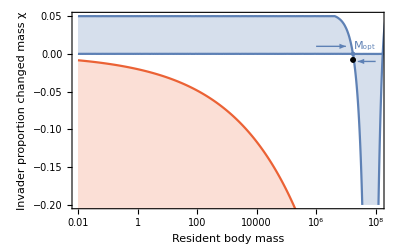

```mathematica
ObsMax=17450000;
MinChi =Table[{Invade[[i]][[1]],Min[Invade[[i]][[2]]]},{i,1,Length[Invade]}];
MaxChi =Table[{Invade[[i]][[1]],Max[Invade[[i]][[2]]]},{i,1,Length[Invade]}];
InvasionPlot=Show[{
ListLogLinearPlot[{MinChi,MaxChi},Filling->{1->{2}},FillingStyle->Directive[ColorData[97,1],Opacity[0.25]],Joined->True,PlotRange->{{10^(-2),1.2*10^8},{-0.2,0.05}},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{"Resident body mass","Invader proportion changed mass χ"}],
ListLogLinearPlot[StarvationThreshold,Joined->True,PlotRange->{-1,0},PlotStyle->ColorData[97,4],Filling->Bottom],
Mopt=Select[MinChi,#[[2]]<0&][[1]][[1]];
ListLogLinearPlot[{{ObsMax,-0.008}},PlotStyle->Directive[{PointSize[Medium],Black}],PlotMarkers->Style["⋀",FontSize->20]],
ListLogLinearPlot[{{Mopt,0}},PlotStyle->Directive[{PointSize[Large],ColorData[97,1]}]],

(*Graphics[{PointSize[Large],Point[{Log@(Mopt),0}]}],
Graphics[{PointSize[Medium],PlotMarkers->".",Red,Point[{Log@(ObsMax),0}]}],*)
Graphics[Text[Style["M_opt",ColorData[97,1]],{Log@(4.5*10^7),0.01}]],
Graphics[{ColorData[97,1],Thick,Arrow[{{Log@(10^6),0.01},{Log@(10^7),0.01}}]}],
Graphics[{ColorData[97,1],Thick,Arrow[{{Log@(10^8),-0.01},{Log@(10^7.4),-0.01}}]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_Invasion.pdf"}],InvasionPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_Invasion.pdf

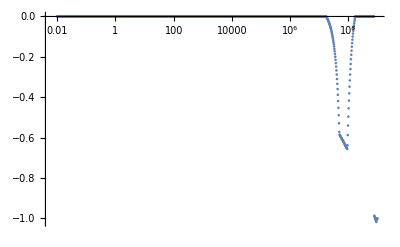

```mathematica
ListLogLinearPlot[MinChi,PlotRange->All]
```

```mathematica
Mopt
```

1.7378×10^7

```mathematica
Mopt=Sort[MinChi,#1[[2]]>#2[[2]]&]
```

{{1.,0.0001},{0.223872,0.0000997277},{0.0234423,0.0000996313},{5.37032,0.0000995792},{6309.57,0.000099568},{12.0226,0.0000995256},{4365.16,0.0000995151},{912011.,0.0000994911},{0.0389045,0.0000993758},{30199.5,0.0000992676},{741.31,0.0000991618},{1.54882×10^7,0.0000991191},{2.29087×10^6,0.0000990836},{1.65959×10^7,0.0000990714},{3162.28,0.0000990337},{87.0964,0.0000989816},{0.239883,0.0000989132},{338.844,0.0000985707},{301995.,0.0000985625},{398.107,0.0000984304},{14.7911,0.0000983341},{794328.,0.0000982819},{0.0199526,0.0000982284},{933254.,0.0000981371},{0.0645654,0.0000980623},{3.38844×10^6,0.0000979736},{0.20893,0.0000979237},{17.7828,0.0000979152},{1949.84,0.00009769},{0.323594,0.0000976066},{123.027,0.0000975823},{3.0903×10^6,0.0000973606},{257040.,0.0000971876},{2511.89,0.0000971488},{85113.8,0.0000971335},{61.6595,0.0000970383},{2.88403,0.0000969049},{3.0903×10^8,0.000096895},{1.25893,0.0000966516},{21.8776,0.0000962599},{2.51189×10^8,0.0000962498},{7.4131×10^8,0.0000959861},{138038.,0.0000958414},{1.12202×10^6,0.0000957282},{13182.6,0.0000956897},{0.0870964,0.0000956816},{891251.,0.0000956008},{0.25704,0.0000954457},{316.228,0.0000952711},{0.831764,0.0000947568},{436516.,0.0000947278},{281838.,0.000094539},{0.134896,0.0000945245},{3715.35,0.0000944381},{186209.,0.0000944353},{0.0371535,0.0000943382},{4073.8,0.0000942922},{870.964,0.0000942782},{9.54993×10^6,0.0000939459},{1.54882×10^6,0.0000939015},{0.416869,0.0000938857},{20893.,0.0000938544},{218776.,0.0000937807},{2.63027×10^8,0.0000937672},{1258.93,0.0000936261},{2137.96,0.0000935572},{0.194984,0.0000935355},{4.16869×10^8,0.0000934548},{24.5471,0.0000933823},{32.3594,0.000093282},{0.120226,0.0000932342},{12302.7,0.0000930211},{0.0112202,0.0000930086},{0.562341,0.000092797},{1.7378×10^6,0.0000927518},{1.25893×10^6,0.000092699},{0.0676083,0.0000925867},{6760.83,0.000092565},{17378.,0.0000925304},{512.861,0.0000924032},{0.630957,0.0000923461},{3.63078,0.0000921771},{89.1251,0.0000920289},{14.1254,0.0000919313},{0.457088,0.0000919001},{0.0275423,0.0000917483},{354813.,0.0000916227},{128825.,0.0000915566},{954993.,0.0000915157},{36307.8,0.0000914802},{363.078,0.0000913449},{4.67735×10^8,0.0000913287},{346737.,0.0000913257},{18.6209,0.0000911882},{1.1749×10^6,0.0000910494},{2.81838×10^6,0.000090939},{3.71535×10^6,0.00009091},{8.91251,0.000090843},{1.65959×10^6,0.0000908145},{0.380189,0.0000906326},{5.12861×10^6,0.0000904865},{11220.2,0.0000904449},{91201.1,0.0000904127},{1047.13,0.0000903272},{5.88844×10^8,0.0000903204},{1122.02,0.0000901083},{60.256,0.0000899999},{8.31764,0.0000899552},{4.67735×10^6,0.0000896091},{4.2658,0.000089602},{478630.,0.0000895323},{3235.94,0.0000895176},{0.0151356,0.0000893079},{7.24436×10^6,0.0000892902},{0.275423,0.0000892901},{0.151356,0.0000892087},{48.9779,0.0000891871},{109648.,0.0000890741},{107152.,0.000088855},{1.23027,0.0000887752},{194.984,0.0000887682},{2.95121,0.0000885943},{0.0354813,0.0000884734},{758.578,0.0000882974},{5888.44,0.0000882251},{0.977237,0.0000881802},{109.648,0.0000881417},{1.23027×10^7,0.0000879791},{0.0169824,0.0000878198},{4677.35,0.0000876323},{7413.1,0.0000876035},{363078.,0.0000875365},{1.47911×10^7,0.0000875064},{2454.71,0.000087424},{60256.,0.0000873453},{1584.89,0.0000872758},{512861.,0.0000869889},{2.45471×10^6,0.0000869219},{27542.3,0.0000868999},{18620.9,0.0000868603},{338844.,0.0000866647},{47863.,0.0000866564},{0.18197,0.0000865967},{870964.,0.000086489},{9.54993,0.000086458},{14791.1,0.0000864382},{0.0134896,0.0000864364},{38018.9,0.0000863554},{436.516,0.0000862219},{0.0707946,0.0000861841},{15488.2,0.0000860345},{0.0223872,0.0000858799},{6.76083×10^6,0.000085864},{112202.,0.0000857866},{2.34423×10^8,0.000085759},{0.107152,0.0000854807},{42.658,0.0000853734},{8.31764×10^6,0.0000852951},{34673.7,0.0000852352},{104713.,0.0000851445},{6.0256,0.0000847573},{0.501187,0.0000845834},{91.2011,0.0000841689},{0.0912011,0.0000840333},{7.76247,0.0000838634},{4.36516×10^8,0.0000834963},{6.60693,0.0000831242},{0.707946,0.000083039},{13.4896,0.0000829709},{138.038,0.0000829045},{6.0256×10^8,0.0000828825},{3.16228×10^6,0.0000825058},{0.346737,0.0000822317},{58.8844,0.0000821192},{0.0190546,0.0000818758},{4.89779,0.0000818447},{0.0338844,0.0000817886},{11.4815,0.0000817873},{19.4984,0.0000817656},{295.121,0.0000815833},{501.187,0.0000809864},{162.181,0.0000808191},{0.0263027,0.0000806791},{1.12202×10^7,0.0000806474},{2.5704×10^6,0.0000805443},{1.20226,0.0000804967},{0.295121,0.000080411},{0.812831,0.0000799041},{5.7544×10^8,0.0000798279},{3.01995,0.0000798088},{977237.,0.0000796039},{239.883,0.0000795368},{0.0120226,0.0000792995},{0.01,0.0000792385},{173.78,0.0000790487},{371535.,0.0000790479},{3.71535,0.0000790228},{114815.,0.0000789771},{181970.,0.0000788806},{0.074131,0.0000788465},{1.07152×10^6,0.0000785871},{6.45654×10^6,0.0000784897},{741310.,0.0000784084},{165959.,0.000078221},{3311.31,0.0000782059},{660693.,0.0000780733},{229.087,0.0000780217},{102329.,0.000077958},{223872.,0.0000778323},{4.16869×10^6,0.0000777614},{5.49541,0.0000776884},{331131.,0.0000776586},{9120.11,0.0000775768},{20417.4,0.0000775293},{5.7544×10^6,0.0000775169},{977.237,0.0000775042},{14125.4,0.0000772556},{22.9087,0.0000772148},{0.169824,0.0000771406},{38.0189,0.0000771361},{9332.54,0.0000767691},{10.2329,0.0000767305},{1202.26,0.0000766754},{251.189,0.000076671},{34.6737,0.0000766337},{125.893,0.0000765931},{8912.51,0.0000761983},{776.247,0.00007607},{8.91251×10^6,0.0000760128},{2398.83,0.0000759956},{0.954993,0.0000759754},{16218.1,0.0000759603},{3.71535×10^8,0.0000757762},{1778.28,0.00007573},{93.3254,0.0000753975},{75857.8,0.0000750236},{5.62341×10^6,0.0000748653},{1.62181×10^7,0.000074802},{2.45471×10^8,0.0000745816},{0.125893,0.0000745338},{2.81838×10^8,0.0000744882},{0.0323594,0.0000742907},{4.0738×10^6,0.000074269},{4.2658×10^6,0.0000742539},{6.76083×10^8,0.000073973},{47.863,0.0000738888},{79432.8,0.000073777},{9549.93,0.0000737656},{891.251,0.0000737465},{245471.,0.0000737026},{389.045,0.0000734547},{151.356,0.0000734391},{57.544,0.0000733999},{707946.,0.0000732464},{0.141254,0.000073199},{42658.,0.0000731427},{0.616595,0.0000731386},{2.75423×10^6,0.0000730168},{4.36516,0.0000729289},{27.5423,0.0000727487},{5.88844×10^6,0.0000727264},{8709.64,0.0000726431},{7.24436,0.0000726354},{6.60693×10^8,0.0000722491},{3801.89,0.0000721868},{851138.,0.0000721786},{218.776,0.000072164},{2089.3,0.0000720616},{112.202,0.000071934},{0.549541,0.0000718414},{1.1749,0.0000718177},{29.5121,0.0000716826},{12.8825,0.0000714751},{0.0954993,0.0000714039},{0.0213796,0.0000713771},{67608.3,0.0000711713},{1.8197×10^6,0.0000709779},{0.0776247,0.0000705655},{3.0903,0.0000705464},{30903.,0.0000705277},{61659.5,0.0000704248},{46773.5,0.0000698928},{416869.,0.00006989},{39810.7,0.0000697609},{1905.46,0.0000696284},{20.4174,0.0000696237},{11481.5,0.000069525},{2.69153×10^8,0.0000694823},{263.027,0.000069386},{0.112202,0.0000693487},{28183.8,0.0000690671},{0.0162181,0.0000689443},{0.0251189,0.0000688351},{0.316228,0.0000687723},{0.0144544,0.0000686771},{117490.,0.0000686302},{0.40738,0.00006856},{9772.37,0.0000685567},{7.24436×10^8,0.0000683773},{489.779,0.0000683098},{295121.,0.0000681143},{186.209,0.0000680071},{0.0107152,0.0000679897},{2.34423×10^6,0.0000679802},{0.446684,0.0000678927},{33113.1,0.0000677194},{1.90546,0.0000676102},{1.94984,0.0000675017},{3.46737×10^8,0.0000674497},{1659.59,0.0000674092},{100000.,0.0000673105},{1.86209,0.0000672817},{25.704,0.0000672814},{147911.,0.0000671546},{7244.36,0.0000669737},{1.99526,0.0000669543},{8511.38,0.0000669208},{1.8197,0.0000665181},{0.234423,0.0000661444},{380189.,0.0000661375},{426.58,0.0000661014},{0.218776,0.0000660822},{0.030903,0.0000659871},{2.04174,0.000065966},{95.4993,0.0000657107},{0.691831,0.0000656182},{3.38844×10^8,0.0000654846},{1.58489×10^6,0.0000653726},{3.80189,0.0000653724},{1.77828,0.0000653213},{331.131,0.0000653002},{41.6869,0.0000652899},{0.158489,0.0000652},{3388.44,0.0000650909},{5.49541×10^6,0.0000648042},{0.018197,0.0000647944},{0.794328,0.0000646798},{4168.69,0.0000645866},{2.0893,0.0000645349},{6165.95,0.0000644803},{1.23027×10^6,0.000064359},{323594.,0.0000643266},{4466.84,0.0000641325},{0.0128825,0.0000640883},{1.7378×10^8,0.0000640577},{0.371535,0.0000640115},{31.6228,0.0000639968},{56.2341,0.0000638455},{3.98107×10^6,0.0000638074},{4.36516×10^6,0.0000637157},{1.7378,0.0000636932},{6606.93,0.0000636193},{0.251189,0.0000635651},{0.204174,0.0000634131},{776247.,0.0000634028},{0.933254,0.0000633874},{131826.,0.0000632884},{72443.6,0.0000631918},{3.16228×10^8,0.0000630114},{12589.3,0.000062905},{2344.23,0.0000628709},{154882.,0.0000628311},{9.33254×10^6,0.0000627811},{1.14815,0.0000627402},{89125.1,0.0000626859},{2.13796,0.0000626591},{7.07946×10^6,0.0000625444},{5248.07,0.0000625334},{794.328,0.0000624736},{1.×10^6,0.0000623786},{5.01187,0.0000620684},{208.93,0.0000620015},{0.0501187,0.0000619664},{0.489779,0.0000619175},{1.69824,0.0000616357},{0.047863,0.0000616106},{354.813,0.0000615982},{10.9648,0.0000615901},{0.0524807,0.0000614465},{2.04174×10^6,0.000061435},{0.0812831,0.000061333},{2.0893×10^6,0.0000612964},{5.12861×10^8,0.0000611364},{10000.,0.0000611327},{3.23594×10^6,0.0000610091},{3.16228,0.0000608048},{6.0256×10^6,0.0000604613},{0.0457088,0.0000603867},{2.18776,0.0000603367},{6.16595,0.0000601708},{2.04174×10^8,0.0000601379},{5.24807×10^8,0.0000601138},{0.0549541,0.0000600432},{4.7863×10^8,0.0000597135},{1412.54,0.0000596252},{177828.,0.0000594651},{83176.4,0.0000593371},{501187.,0.000059177},{1.65959,0.0000591506},{8317.64,0.0000590408},{5495.41,0.0000587756},{19952.6,0.0000586562},{13489.6,0.0000585701},{309.03,0.0000585227},{5011.87,0.0000584179},{1071.52,0.0000583784},{0.269153,0.0000583095},{0.0436516,0.0000583023},{0.190546,0.000058171},{18197.,0.0000579062},{229087.,0.0000578679},{0.1,0.0000577846},{46.7735,0.0000577843},{1348.96,0.0000577805},{0.057544,0.0000577487},{1.34896×10^7,0.0000577416},{275.423,0.0000576428},{2.23872,0.0000575656},{8.51138,0.0000574994},{12.3027,0.0000574658},{6.16595×10^8,0.0000574356},{6.91831×10^8,0.0000572895},{141.254,0.0000570281},{8.51138×10^6,0.000056896},{0.0295121,0.0000568846},{9.12011,0.0000566373},{141254.,0.0000566307},{3.46737×10^6,0.000056376},{6.76083,0.0000563383},{1.62181,0.0000562398},{0.0239883,0.0000562232},{16982.4,0.0000561304},{0.0204174,0.0000561295},{4.46684,0.0000557441},{1.99526×10^6,0.0000554614},{23.9883,0.0000553659},{0.0416869,0.000055365},{1479.11,0.0000553343},{0.0114815,0.0000552713},{5.62341,0.0000552631},{575440.,0.0000551194},{97.7237,0.0000551046},{2.13796×10^6,0.000055019},{0.131826,0.0000547903},{114.815,0.0000547784},{21.3796,0.0000547386},{120226.,0.0000547303},{128.825,0.000054635},{0.060256,0.0000545553},{588844.,0.0000544143},{478.63,0.0000543789},{2.29087,0.0000543439},{0.338844,0.0000543376},{1148.15,0.0000537741},{0.60256,0.0000535784},{54.9541,0.0000534597},{1.38038×10^7,0.0000534034},{1.31826×10^7,0.0000533302},{1.12202,0.0000532657},{97723.7,0.0000532172},{3.54813×10^8,0.0000532008},{37.1535,0.0000531598},{7.94328,0.0000531347},{15.8489,0.0000530932},{16.5959,0.0000530028},{1.58489,0.0000529052},{3.63078×10^6,0.000052874},{263027.,0.0000527549},{831764.,0.0000526922},{6.45654×10^8,0.0000521984},{0.11749,0.000052196},{912.011,0.0000518094},{0.0398107,0.000051582},{10232.9,0.0000514839},{5.62341×10^8,0.0000514832},{275423.,0.0000514488},{3.89045,0.0000512237},{0.0851138,0.0000511405},{5.01187×10^6,0.0000511094},{562341.,0.0000510196},{0.147911,0.0000508073},{2.34423,0.0000506696},{4.7863×10^6,0.0000506391},{3.23594,0.0000505822},{15.1356,0.0000505693},{0.537032,0.0000505407},{9.77237,0.0000504792},{0.0630957,0.000050455},{0.912011,0.0000504178},{0.177828,0.0000503894},{63095.7,0.000050361},{0.288403,0.0000503422},{446684.,0.0000503179},{17.378,0.0000502752},{1.41254×10^6,0.0000502747},{3467.37,0.0000501645},{45708.8,0.0000501466},{1.38038×10^6,0.0000500582},{1000.,0.0000498837},{1288.25,0.0000498537},{33.8844,0.0000496038},{0.0154882,0.0000493621},{1.54882,0.0000491486},{0.776247,0.0000490853},{8128.31,0.0000490125},{1.86209×10^8,0.0000489509},{1.20226×10^7,0.0000489494},{2041.74,0.0000489138},{602560.,0.0000488831},{389045.,0.0000487861},{2.69153×10^6,0.0000486248},{28840.3,0.0000485253},{1.90546×10^8,0.0000485173},{676083.,0.0000480926},{3890.45,0.0000480841},{2290.87,0.0000480573},{165.959,0.0000479183},{0.676083,0.000047837},{1.51356×10^7,0.0000477843},{467735.,0.0000477402},{199.526,0.0000475717},{812.831,0.0000475023},{3.31131×10^8,0.0000473762},{5.37032×10^6,0.000047366},{0.0138038,0.0000473549},{380.189,0.0000472783},{5754.4,0.0000470754},{0.017378,0.0000469906},{0.0281838,0.0000469903},{0.0380189,0.0000469609},{4.2658×10^8,0.0000469081},{316228.,0.0000466873},{2.39883,0.0000465408},{4786.3,0.0000464978},{3.89045×10^6,0.0000464068},{11749.,0.000046321},{1.14815×10^6,0.0000461283},{4.46684×10^6,0.0000461162},{14.4544,0.0000454538},{0.0660693,0.0000454398},{1.14815×10^7,0.0000452462},{1.51356,0.0000449719},{18.197,0.0000448872},{1548.82,0.000044854},{1.44544×10^6,0.0000447924},{416.869,0.0000447591},{1.69824×10^6,0.0000447341},{5.01187×10^8,0.0000446931},{40.738,0.000044421},{7079.46,0.0000442512},{1.34896×10^6,0.0000441676},{7.4131,0.0000436113},{154.882,0.0000435751},{100.,0.000043575},{0.436516,0.0000435535},{162181.,0.0000435296},{1.94984×10^6,0.0000434024},{1.09648,0.000043396},{0.104713,0.0000431668},{177.828,0.000043071},{0.398107,0.0000429083},{0.0229087,0.0000428499},{2.18776×10^6,0.0000425758},{0.0102329,0.0000423177},{53.7032,0.0000422463},{549541.,0.0000421358},{2.45471,0.0000419554},{5.12861,0.0000417669},{41686.9,0.0000415959},{5.37032×10^8,0.0000415487},{0.0363078,0.0000415088},{1.58489×10^7,0.0000414714},{288.403,0.0000414024},{1737.8,0.0000412162},{0.0123027,0.0000410637},{11.749,0.0000409652},{45.7088,0.000040877},{6.16595×10^6,0.0000406888},{1.47911,0.0000403769},{37153.5,0.0000403453},{1.41254×10^7,0.0000402772},{1.28825×10^7,0.0000402073},{0.0194984,0.0000401436},{0.165959,0.0000401015},{0.0891251,0.0000399796},{1862.09,0.0000399431},{3.31131,0.0000398762},{1.09648×10^6,0.0000398733},{1.02329×10^6,0.0000398162},{2.18776×10^8,0.0000397995},{35481.3,0.0000397727},{0.30903,0.0000396274},{10471.3,0.0000396005},{0.0691831,0.0000395018},{28.8403,0.0000394358},{467.735,0.0000391993},{31622.8,0.0000390311},{10.4713,0.0000389554},{0.47863,0.000038914},{616595.,0.0000385047},{69183.1,0.0000383957},{26.9153,0.0000383146},{1.02329×10^7,0.0000381331},{4.57088,0.0000380456},{13.8038,0.0000377695},{2.39883×10^8,0.0000377292},{616.595,0.0000377183},{23988.3,0.0000376691},{630.957,0.0000375457},{251189.,0.0000374974},{15135.6,0.0000374399},{123027.,0.0000372618},{19498.4,0.0000372463},{22.3872,0.0000370863},{0.363078,0.00003707},{0.891251,0.0000370683},{2.51189×10^6,0.0000369119},{2.51189,0.0000369114},{23442.3,0.000036868},{7943.28,0.0000368453},{19.0546,0.0000368153},{2.23872×10^8,0.0000367286},{117.49,0.0000366707},{602.56,0.0000365805},{3.98107,0.0000365745},{0.0269153,0.000036311},{1.04713×10^7,0.0000363061},{3.98107×10^8,0.0000362468},{173780.,0.0000362054},{645.654,0.000036057},{6.60693×10^6,0.0000359968},{1230.27,0.0000358978},{24547.1,0.000035843},{95499.3,0.0000356932},{1.44544,0.0000353654},{0.0346737,0.0000352331},{6.30957,0.0000350381},{1.8197×10^8,0.000034977},{1.77828×10^6,0.0000348417},{426580.,0.0000345786},{588.844,0.000034138},{0.123027,0.0000340138},{0.138038,0.0000339945},{30.903,0.0000339663},{234423.,0.00003387},{0.588844,0.0000336671},{1.94984×10^8,0.0000336129},{1.47911×10^6,0.0000335861},{22908.7,0.0000334512},{288403.,0.0000334336},{3548.13,0.0000334189},{660.693,0.0000332465},{1.07152,0.0000331329},{0.758578,0.0000331224},{0.229087,0.0000330821},{14454.4,0.00003304},{4265.8,0.000032997},{3.31131×10^6,0.0000328415},{3.89045×10^8,0.0000326384},{0.0724436,0.0000326327},{1.31826×10^6,0.0000326278},{6456.54,0.0000326173},{5.7544,0.0000323011},{15848.9,0.0000322115},{0.213796,0.0000321472},{131.826,0.0000317037},{1.×10^7,0.0000316579},{87096.4,0.000031588},{2238.72,0.0000315623},{2.5704,0.0000314069},{134896.,0.0000313886},{0.245471,0.0000313872},{25118.9,0.0000313783},{831.764,0.00003115},{102.329,0.0000311181},{1.62181×10^6,0.0000310188},{323.594,0.0000308653},{25.1189,0.0000306885},{346.737,0.0000306718},{2.39883×10^6,0.0000306022},{0.0109648,0.0000305812},{1.20226×10^6,0.0000304677},{12882.5,0.0000304646},{575.44,0.0000303967},{52.4807,0.0000302087},{144.544,0.0000301612},{1.41254,0.0000299392},{2.75423×10^8,0.0000297452},{0.660693,0.0000296969},{38904.5,0.0000294981},{234.423,0.0000293244},{676.083,0.0000291082},{0.0147911,0.0000290793},{6.91831,0.0000289965},{190.546,0.0000289118},{0.524807,0.0000288965},{0.0218776,0.000028722},{3.38844,0.0000286848},{245.471,0.0000286539},{0.199526,0.0000286166},{537032.,0.0000284889},{0.0165959,0.0000284708},{933.254,0.0000284608},{36.3078,0.000028415},{724436.,0.0000283373},{0.0331131,0.0000281408},{1621.81,0.0000281299},{6.91831×10^6,0.0000280578},{812831.,0.0000280525},{2.13796×10^8,0.0000280149},{33884.4,0.00002788},{0.0933254,0.0000278418},{0.109648,0.0000275417},{13.1826,0.0000275385},{44668.4,0.0000274309},{22387.2,0.0000274301},{6025.6,0.000027363},{0.154882,0.00002734},{64565.4,0.00002714},{0.263027,0.0000270276},{398107.,0.0000269741},{4570.88,0.000026841},{489779.,0.0000266847},{17782.8,0.0000264593},{1.07152×10^7,0.0000261406},{0.331131,0.0000261288},{77624.7,0.0000260422},{19.9526,0.000026036},{223.872,0.0000256333},{10715.2,0.0000254728},{2.63027,0.0000254398},{562.341,0.000025362},{0.0131826,0.0000253472},{1.90546×10^6,0.0000252845},{53703.2,0.000025276},{29512.1,0.0000252628},{1096.48,0.0000249743},{0.025704,0.0000248535},{0.0758578,0.0000248244},{309030.,0.0000247597},{8.70964,0.0000244628},{25704.,0.0000242632},{1995.26,0.0000241209},{1.38038,0.0000241002},{2.23872×10^6,0.0000239397},{54954.1,0.0000238676},{691.831,0.0000236365},{52480.7,0.0000236226},{257.04,0.0000235833},{9.12011×10^6,0.0000234582},{758578.,0.0000234376},{0.0186209,0.0000234258},{0.870964,0.0000233405},{630957.,0.0000232578},{4.0738×10^8,0.0000232099},{44.6684,0.0000231704},{457.088,0.0000227763},{39.8107,0.0000227702},{7.76247×10^6,0.000022742},{3.63078×10^8,0.0000226667},{5.24807×10^6,0.0000225827},{74.131,0.000022574},{7762.47,0.0000225486},{0.186209,0.0000225243},{1.04713,0.0000224781},{72.4436,0.0000224087},{407.38,0.0000222003},{3981.07,0.000022122},{7.07946×10^8,0.0000221179},{3.80189×10^6,0.0000220976},{11.2202,0.0000219948},{75.8578,0.0000218631},{9.33254,0.0000218431},{8.12831,0.0000218328},{33.1131,0.0000218188},{4.57088×10^6,0.0000214244},{4.0738,0.0000214227},{70.7946,0.0000213711},{5.24807,0.0000209379},{1023.29,0.0000208268},{12022.6,0.0000208231},{74131.,0.0000207354},{301.995,0.0000206251},{8.70964×10^6,0.0000204803},{77.6247,0.0000202721},{0.0316228,0.0000202392},{0.281838,0.0000199681},{2818.38,0.0000199546},{371.535,0.0000199067},{4.67735,0.0000198311},{69.1831,0.000019465},{6918.31,0.0000194453},{7.58578×10^6,0.0000194232},{56234.1,0.0000193838},{2884.03,0.0000192992},{13803.8,0.0000190955},{549.541,0.0000190397},{2.69153,0.0000190081},{51286.1,0.0000189207},{0.42658,0.000018884},{2754.23,0.000018861},{21877.6,0.000018816},{2.29087×10^8,0.0000187369},{1.25893×10^7,0.000018411},{1.44544×10^7,0.0000183245},{81283.1,0.0000182134},{7.94328×10^6,0.0000181834},{1.34896,0.0000178501},{79.4328,0.0000177973},{2.63027×10^6,0.0000177913},{199526.,0.000017764},{104.713,0.0000177296},{204174.,0.000017705},{213.796,0.0000176185},{120.226,0.0000176067},{0.011749,0.0000173685},{51.2861,0.0000173506},{16595.9,0.0000172701},{2.95121×10^8,0.0000171417},{3.46737,0.000017006},{0.389045,0.000016932},{9.77237×10^6,0.0000169168},{2951.21,0.0000168871},{151356.,0.0000168569},{707.946,0.0000168255},{0.74131,0.0000167926},{67.6083,0.0000166941},{23.4423,0.0000166424},{1.51356×10^6,0.0000166309},{125893.,0.0000162092},{0.0794328,0.0000160687},{2691.53,0.000016026},{1174.9,0.0000159653},{0.467735,0.0000155744},{1.28825×10^6,0.0000154634},{3.01995×10^8,0.0000149153},{3630.78,0.0000148461},{0.128825,0.000014793},{12.5893,0.0000147832},{93325.4,0.0000147534},{0.0977237,0.0000147185},{26302.7,0.0000144862},{81.2831,0.0000144347},{1.69824×10^7,0.0000142396},{269.153,0.0000140741},{7.58578,0.0000140214},{169.824,0.0000139963},{10.,0.0000139043},{0.17378,0.0000139037},{6.30957×10^8,0.0000139006},{194984.,0.000013894},{0.020893,0.000013846},{144544.,0.0000137405},{208930.,0.0000136996},{851.138,0.0000134107},{0.57544,0.0000134061},{2187.76,0.0000133932},{6.30957×10^6,0.000013376},{19054.6,0.0000133107},{3.23594×10^8,0.0000131951},{691831.,0.0000131576},{66.0693,0.0000130622},{3019.95,0.0000127107},{158.489,0.0000127032},{0.0245471,0.0000126247},{20.893,0.0000125256},{3.80189×10^8,0.0000124574},{0.144544,0.000012137},{2.75423,0.0000121098},{0.0489779,0.0000118974},{1.04713×10^6,0.0000118936},{0.0512861,0.0000118164},{57544.,0.0000118112},{5370.32,0.0000116429},{0.0301995,0.0000115353},{2630.27,0.0000114573},{5128.61,0.0000114555},{537.032,0.0000114355},{1.02329,0.0000114332},{0.645654,0.0000111994},{1.31826,0.0000111908},{50118.7,0.0000111835},{0.0467735,0.0000111067},{0.114815,0.0000109005},{4.89779×10^8,0.0000108602},{0.0537032,0.0000108557},{83.1764,0.0000101805},{0.301995,0.0000101732},{524807.,0.0000100997},{0.354813,9.80963×10^-6},{1380.38,9.4664×10^-6},{0.0446684,9.45161×10^-6},{6.45654,9.35666×10^-6},{0.0158489,9.24118×10^-6},{0.851138,9.23616×10^-6},{169824.,9.11852×10^-6},{10964.8,9.09091×10^-6},{0.0562341,9.00784×10^-6},{5.88844,8.79996×10^-6},{724.436,8.66919×10^-6},{1819.7,8.64133×10^-6},{64.5654,8.57313×10^-6},{7.4131×10^6,8.26115×10^-6},{1445.44,8.25004×10^-6},{0.0141254,8.10205×10^-6},{3.54813×10^6,8.01937×10^-6},{134.896,7.79499×10^-6},{21379.6,7.62038×10^-6},{1.09648×10^7,7.59991×10^-6},{2.95121×10^6,7.2604×10^-6},{40738.,7.13103×10^-6},{0.042658,6.93981×10^-6},{0.512861,6.91025×10^-6},{3090.3,6.76212×10^-6},{1.77828×10^8,6.6584×10^-6},{28.1838,6.45682×10^-6},{0.0831764,6.35725×10^-6},{0.0588844,6.26488×10^-6},{7585.78,6.13155×10^-6},{190546.,6.11207×10^-6},{181.97,6.05865×10^-6},{0.0177828,5.9824×10^-6},{239883.,5.82079×10^-6},{4.57088×10^8,5.78105×10^-6},{4.16869,5.7659×10^-6},{213796.,5.73066×10^-6},{8.12831×10^6,5.71264×10^-6},{3.01995×10^6,5.6025×10^-6},{5.49541×10^8,5.36426×10^-6},{204.174,5.3177×10^-6},{0.0104713,5.23499×10^-6},{2570.4,5.16238×10^-6},{446.684,5.11537×10^-6},{1698.24,5.10698×10^-6},{158489.,5.0608×10^-6},{85.1138,5.03078×10^-6},{7.58578×10^8,4.86273×10^-6},{3.54813,4.83745×10^-6},{32359.4,4.76576×10^-6},{2.81838,4.74274×10^-6},{43.6516,4.66806×10^-6},{1318.26,4.574×10^-6},{4.89779×10^6,4.483×10^-6},{269153.,4.18134×10^-6},{1.99526×10^8,4.17433×10^-6},{1.28825,4.12403×10^-6},{5623.41,3.92266×10^-6},{954.993,3.69445×10^-6},{50.1187,3.67552×10^-6},{2.88403×10^8,3.64313×10^-6},{0.040738,3.57872×10^-6},{4897.79,3.42916×10^-6},{107.152,3.40546×10^-6},{16.2181,3.37622×10^-6},{63.0957,3.23057×10^-6},{30.1995,3.19378×10^-6},{26.3027,3.15781×10^-6},{4.46684×10^8,3.14537×10^-6},{645654.,3.12117×10^-6},{35.4813,2.90521×10^-6},{0.162181,2.78759×10^-6},{2.5704×10^8,2.66729×10^-6},{0.0125893,2.66015×10^-6},{0.0616595,2.619×10^-6},{524.807,2.55476×10^-6},{70794.6,2.40725×10^-6},{2.88403×10^6,2.36303×10^-6},{147.911,2.29971×10^-6},{15.4882,2.15657×10^-6},{0.0288403,2.036×10^-6},{26915.3,2.03573×10^-6},{16.9824,1.97012×10^-6},{43651.6,1.75864×10^-6},{2.0893×10^8,1.43947×10^-6},{1.1749×10^7,1.35928×10^-6},{457088.,1.32869×10^-6},{58884.4,1.13624×10^-6},{1.86209×10^6,1.13426×10^-6},{4.7863,1.09817×10^-6},{7.07946,1.09636×10^-6},{1513.56,8.71237×10^-7},{66069.3,7.48102×10^-7},{407380.,6.8191×10^-7},{0.102329,6.01038×10^-7},{10.7152,5.76104×10^-7},{48977.9,4.24317×10^-7},{38.9045,3.4073×10^-7},{0.724436,9.76262×10^-8},{281.838,8.72438×10^-8},{1.7378×10^7,-0.000679733},{1.77828×10^7,-0.00318289},{1.8197×10^7,-0.00579526},{1.69824×10^8,-0.00629276},{1.86209×10^7,-0.0085169},{1.90546×10^7,-0.0114478},{1.94984×10^7,-0.0144881},{1.65959×10^8,-0.0151637},{1.99526×10^7,-0.0177378},{2.04174×10^7,-0.0210969},{1.62181×10^8,-0.0246488},{2.0893×10^7,-0.0246654},{2.13796×10^7,-0.0283435},{2.18776×10^7,-0.0323311},{1.58489×10^8,-0.0349479},{2.23872×10^7,-0.0364283},{2.29087×10^7,-0.0408352},{2.34423×10^7,-0.0454517},{1.54882×10^8,-0.046061},{2.39883×10^7,-0.0503779},{2.45471×10^7,-0.0555139},{1.51356×10^8,-0.057888},{2.51189×10^7,-0.0609597},{2.5704×10^7,-0.0668154},{1.47911×10^8,-0.0707288},{2.63027×10^7,-0.0728809},{2.69153×10^7,-0.0793564},{1.44544×10^8,-0.0844835},{2.75423×10^7,-0.0862418},{2.81838×10^7,-0.0936373},{1.41254×10^8,-0.0991518},{2.88403×10^7,-0.101343},{2.95121×10^7,-0.109658},{1.38038×10^8,-0.114834},{3.01995×10^7,-0.118384},{3.0903×10^7,-0.12782},{1.34896×10^8,-0.13173},{3.16228×10^7,-0.137766},{3.23594×10^7,-0.148523},{1.31826×10^8,-0.149739},{3.31131×10^7,-0.15989},{1.28825×10^8,-0.168961},{3.38844×10^7,-0.172167},{3.46737×10^7,-0.185255},{1.25893×10^8,-0.189598},{3.54813×10^7,-0.199353},{1.23027×10^8,-0.211647},{3.63078×10^7,-0.214461},{3.71535×10^7,-0.230681},{1.20226×10^8,-0.23521},{3.80189×10^7,-0.24821},{1.1749×10^8,-0.260486},{3.89045×10^7,-0.267051},{1.14815×10^8,-0.287475},{3.98107×10^7,-0.287502},{4.0738×10^7,-0.309564},{1.12202×10^8,-0.316478},{4.16869×10^7,-0.333537},{1.09648×10^8,-0.347493},{4.2658×10^7,-0.35952},{1.07152×10^8,-0.380722},{4.36516×10^7,-0.387815},{1.04713×10^8,-0.416463},{4.46684×10^7,-0.41852},{4.57088×10^7,-0.452036},{1.02329×10^8,-0.454818},{4.67735×10^7,-0.488664},{1.×10^8,-0.495885},{4.7863×10^7,-0.528502},{9.77237×10^7,-0.539965},{4.89779×10^7,-0.571952},{5.01187×10^7,-0.585613},{9.54993×10^7,-0.587258},{5.12861×10^7,-0.588185},{5.24807×10^7,-0.590768},{5.37032×10^7,-0.593362},{5.49541×10^7,-0.595968},{5.62341×10^7,-0.598586},{5.7544×10^7,-0.601215},{5.88844×10^7,-0.603855},{6.0256×10^7,-0.606507},{6.16595×10^7,-0.609171},{6.30957×10^7,-0.611846},{6.45654×10^7,-0.614533},{6.60693×10^7,-0.617232},{6.76083×10^7,-0.619942},{6.91831×10^7,-0.622665},{7.07946×10^7,-0.625399},{7.24436×10^7,-0.628146},{7.4131×10^7,-0.630904},{7.58578×10^7,-0.633675},{7.76247×10^7,-0.636458},{9.33254×10^7,-0.637763},{7.94328×10^7,-0.639253},{8.12831×10^7,-0.64206},{8.31764×10^7,-0.644879},{8.51138×10^7,-0.647711},{8.70964×10^7,-0.650555},{8.91251×10^7,-0.653412},{9.12011×10^7,-0.656281},{7.76247×10^8,-0.986305},{7.94328×10^8,-0.990634},{8.12831×10^8,-0.994982},{8.31764×10^8,-0.999349},{1.×10^9,-1.00018},{9.77237×10^8,-1.00066},{9.54993×10^8,-1.00195},{8.51138×10^8,-1.00373},{8.70964×10^8,-1.00814},{9.33254×10^8,-1.00817},{8.91251×10^8,-1.01256},{9.12011×10^8,-1.01701}}

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
```

```mathematica
Log10@3981.071705534969
```

3.6

```mathematica
Median[Log10@data[[All,1]]]
Mean[Log10@data[[All,1]]]
```

3.0086

3.06209

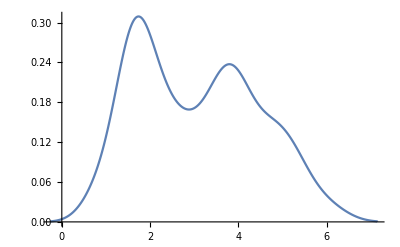

```mathematica
SmoothHistogram[Log10@data[[All,1]]]
```

```mathematica
mm=Table[10^x,{x,0,8,0.001}];
```

```mathematica
mm[[6927]]
```

8.43335×10^6

```mathematica
MinBM=Table[{(10^MassExp),(1+MinMass)*(10^MassExp)^1.19},{MassExp,-2,9,0.01}];
MaxBM=Table[{10^MassExp,MinMass*10^MassExp},{MassExp,-2,9,0.01}]
```

{{0.01,{{0.0001,5.79238×10^-6},{0.000102329,5.42318×10^-6},{0.000104713,5.05235×10^-6},{0.000107152,4.6799×10^-6},1093,{9.33254×10^6,-0.00217472},{9.54993×10^6,-0.00238955},{9.77237×10^6,-0.00259458},{1.×10^7,-0.0028098}}},1099,{1.×10^9,{1}}}
 |  |  |  |

```mathematica
Show[{
ListLogLogPlot[MinBM],
ListLogLogPlot[MaxBM]
}]
```

-Graphics-